```mathematica
ClearAll["Global`*"];Clear[Derivative];
```

```mathematica
Import[NotebookDirectory[]<>"lattice.wl"];
```

```mathematica
L=4;
d=2;
```

```mathematica
lattice=getLattice[L,d];
```

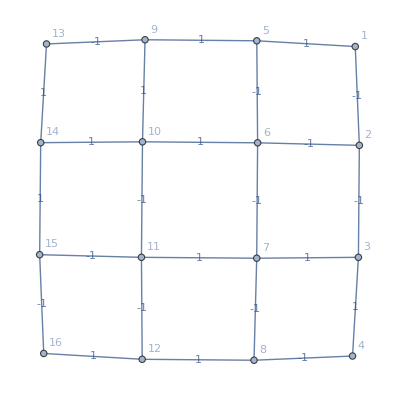

```mathematica
lattice=Fold[SetProperty[{#1,#2},VertexLabels->#2]&,lattice,VertexList[lattice]];

lattice=Fold[SetProperty[{#1,#2},EdgeLabels->PropertyValue[{#1,#2},EdgeCapacity]]&,lattice,EdgeList[lattice]]
```

```mathematica
{#,nextVertex[#,1,L]}&/@VertexList[lattice]
```

{{3,4},{7,8},{5,6},{9,10},{10,11},{14,15},{4,False},{13,14},{6,7},{11,12},{1,2},{15,16},{12,False},{16,False},{8,False},{2,3}}

```mathematica
{#,previousVertex[#,1,L]}&/@VertexList[lattice]
```

{{3,2},{7,6},{5,False},{9,False},{10,9},{14,13},{4,3},{13,False},{6,5},{11,10},{1,False},{15,14},{12,11},{16,15},{8,7},{2,1}}

```mathematica
{#,nextVertex[#,2,L]}&/@VertexList[lattice]
```

{{3,7},{7,11},{5,9},{9,13},{10,14},{14,False},{4,8},{13,False},{6,10},{11,15},{1,5},{15,False},{12,16},{16,False},{8,12},{2,6}}

```mathematica
{#,previousVertex[#,2,L]}&/@VertexList[lattice]
```

{{3,False},{7,3},{5,1},{9,5},{10,6},{14,10},{4,False},{13,9},{6,2},{11,7},{1,False},{15,11},{12,8},{16,12},{8,4},{2,False}}

```mathematica
(*Function to map Plaquettes as lists of edges 
LabelPlaquettes[L_,d_]:=*)
```

```mathematica
Subsets[Range[1,3],{2}]
```

{{1,2},{1,3},{2,3}}